## Inicialize some functions

```mathematica
<<CompiledFunctionTools`;
Needs["NumericalCalculus`"]
<<MaTeX`
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"}
exportOptions={"AllowRasterization"->True,ImageSize->340,ImageResolution->800};
```

{PerformanceGoal→Quality,PlotRange→Full,FrameLabel→{-Graphics-,-Graphics-},{BaseStyle→Directive[FontSize→12],AxesStyle→Directive[FontSize→12],TicksStyle→Directive[FontSize→12],LabelStyle→{FontFamily→Latin Modern Roman,FontSize→12},BaseStyle→texStyle},ColorFunction→SunsetColors}

## Defining the Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
as={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

# N = 3

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2+1/3 (-(7 λ)/4-χ^2),-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/2+1/3 (-(7 λ)/4-4 χ^2),-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2+1/3 (-(3 λ)/4-9 χ^2)}}

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Geodesics

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

### Initial value problem

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solMultileft=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,15},PrecisionGoal->3,AccuracyGoal->3],{i,π-0.225,π+0.225,0.01}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4104.53,1.37037×10^6},{1.37037×10^6,4.57525×10^8}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.09032×10^-12,-4.14912×10^-8},{-4.14912×10^-8,0.000213692}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.99013×10^-12,-4.11771×10^-8},{-4.11771×10^-8,0.000213101}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at Notebook$$16$52460`t == 3.50483; unable to continue.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.89139×10^6,-1.38267×10^7},{-1.38267×10^7,6.61199×10^7}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"savedData/solMulti_N=3_mintheta=2.43.m",solMultileft]
```

/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_mintheta=2.43.m

```mathematica
solMulti=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,10},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.63,0.01}];
```

```mathematica
Export[NotebookDirectory[]<>"savedData/solMulti_N=3_maxtheta=0,63.m",solMulti]
```

/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_maxtheta=0,63.m

```mathematica
solMulti1=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,10},PrecisionGoal->2,AccuracyGoal->2],{i,-0.63,0,0.01}];
```

```mathematica
Export[NotebookDirectory[]<>"savedData/solMulti_N=3_maxtheta=-0,63.m",solMulti1]
```

/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_maxtheta=-0,63.m

```mathematica
solMultibottom=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[i,0,0,1]],{λ,χ},{t,0,10},PrecisionGoal->4,AccuracyGoal->4],{i,-1,1,0.04}];
```

```mathematica
Export[NotebookDirectory[]<>"solMulti_N=3_maxtheta=0,63.m",solMultibottom]
```

```mathematica
geodIn=Quiet@NDSolve[Join[eq,cauchy[0,0,Cos[π-0.225],Sin[π-0.225]]],{λ,χ},{t,0,15},PrecisionGoal->3,AccuracyGoal->3]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

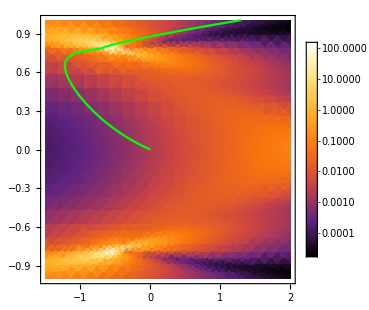

```mathematica
pl1=ParametricPlot[{λ[t],χ[t]}/.geodIn,{t,0,12},PlotRange->All,Frame->True,PlotStyle->Green];
plt=Show[{geodbg,pl1}, ImageSize->310]
```

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-1.5,2},{χ,-1,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->20];
```